# PAPER MALTONI: CALCULO RATA DE DECAIMIENTO

#### Definición de X_R, Y_R y Z_R

```mathematica
Subscript[X, R] = -1;
Subscript[Y, R]=-2 ;
Subscript[Z, R]= -2;
```

#### Valores de las masas

```mathematica
Subscript[M, c]= 1.5; (*GeV*)
Subscript[M, b]= 4.8; (*GeV*)
```

#### Valor de η

```mathematica
η = 4*(Subscript[M, c]/Subscript[M, b])^2;
```

#### Definición de μ

```mathematica
μbar =2*Subscript[M, c];
```

#### Constantes

```mathematica
κp = 0 ;
κm = 0 ;
Subscript[n, f] = 5;
Subscript[β, 0] = 11 - (2/3)*Subscript[n, f]
Subscript[β, 1] = 102 - (38/3)*Subscript[n, f]
Subscript[Λ, 6]=1/(Exp[6.9523614550296/2]/(4.8))
Subscript[Λ, 5]= 1/(Exp[5.9851843934935/2]/(4.8))
Λ = 0.2407548028830499; (*GeV*)
Mw = 80.385; (*GeV*)
```

23/3

116/3

0.148441

0.240755

#### Valor de Λ

```mathematica
(*Subscript[α, s][4.8] = 0.22;
x = Log[(4.8)^2/Λ^2];
Subscript[Λ, 1]= Solve[0.22 - ((4*Pi/(Subscript[β, 0]*x))*(1-(Subscript[β, 1]*Log[x]/(Subscript[β, 0]^2*x))))==0,x];
y = Log[(91.1876)^2/Λ^2];
Subscript[Λ, 2]= Solve[0.1184 - ((4*Pi/(Subscript[β, 0]*y))*(1- (Subscript[β, 1]*Log[y]/(Subscript[β, 0]^2*y))))==0,y];*)
```

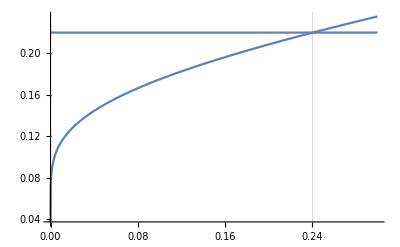

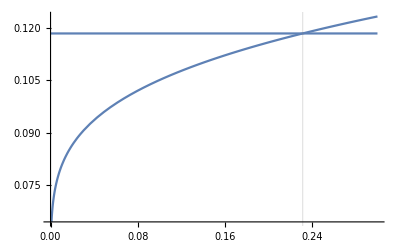

```mathematica
func1[Λ_] := (4*Pi/(Subscript[β, 0]*Log[(4.8)^2/Λ^2]))*(1- (Subscript[β, 1]*Log[Log[(4.8)^2/Λ^2]]/(Subscript[β, 0]^2*Log[(4.8)^2/Λ^2])));
func2[Λ_] := (4*Pi/(Subscript[β, 0]*Log[(91.1876)^2/Λ^2]))*(1- (Subscript[β, 1]*Log[Log[(91.1876)^2/Λ^2]]/(Subscript[β, 0]^2*Log[(91.1876)^2/Λ^2])));
p1 =Plot[func1[Λ],{Λ,0,0.3}, GridLines -> {{0.2405},None}];
p2 = Plot[0.22,{Λ,0,0.3}];
Show[p1,p2]
p3 = Plot[func2[Λ],{Λ,0,0.3},GridLines -> {{0.2315},None}];
p4 = Plot[0.1184,{Λ,0,0.3}];
Show[p3,p4]
```

#### Valor de α_s

```mathematica
Subscript[α, s][μ_] := (4*Pi/(Subscript[β, 0]*Log[μ^2/Λ^2]))*(1- Subscript[β, 1]*Log[Log[μ^2/Λ^2]]/(Subscript[β, 0]^2*Log[μ^2/Λ^2]))
Subscript[α, s][4.8]
```

0.22

#### Calculo de C1 y C8

```mathematica
γp0 = 2*(3-1);
γm0 = -2*(3+1);
γp1 = (3-1)/6*(-21 + (4/3)*Subscript[n, f] - 2*Subscript[β, 0]*κp);
γm1 = (3+1)/6*(-21 - (4/3)*Subscript[n, f] - 2*Subscript[β, 0]*κm);
Jp = γp0*Subscript[β, 1]/(2*Subscript[β, 0]^2) - γp1/(2*Subscript[β, 0]);
Jm = γm0*Subscript[β, 1]/(2*Subscript[β, 0]^2) - γm1/(2*Subscript[β, 0]);
Bp = (3-1)/6*(11+ κp);
Bm = (3+1)/6*(-11 + κm);
```

```mathematica
Cp[μ_] := (Subscript[α, s][Mw]/Subscript[α, s][μ])^(γp0/(2*Subscript[β, 0]))*(1 + Subscript[α, s][μ]/(4*Pi)*Bp)*(1+(Subscript[α, s][Mw]-Subscript[α, s][μ])/(4*Pi)*(Bp-Jp));

Cm[μ_] := (Subscript[α, s][Mw]/Subscript[α, s][μ])^(γm0/(2*Subscript[β, 0]))*(1 + Subscript[α, s][μ]/(4*Pi)*Bm)*(1+(Subscript[α, s][Mw]-Subscript[α, s][μ])/(4*Pi)*(Bm-Jm));
```

#### C_1 y C_8

```mathematica
Subscript[C, 1][μ_] := 2*Cp[μ]-Cm[μ]
Subscript[C, 8][μ_] := Cp[μ]+Cm[μ]
```

```mathematica
Subscript[C, 1][4.8]
Subscript[C, 8][4.8]
```

0.55032

2.14019

```mathematica
C1LO = 0.41;
C8LO = 2.19;
```

#### Definiciones de los Diferentes Γ_0

```mathematica
Subscript[V, cb] = 0.814*0.2257^2; (*Wolfenstein parameters*)
Subscript[G, F] = 1.1663787*10^(-5); (*GeV-2*)
Subscript[Γ, 0] = (Subscript[G, F]^2*Subscript[V, cb]^2*Subscript[M, b]^3)/(432*Pi*Subscript[M, c])
Γ0D = (Subscript[G, F]^2*Subscript[V, cb]^2*Subscript[M, b]^3)/(257*Pi*Subscript[M, c])
```

1.27073×10^-14

2.13601×10^-14

## Leading Order

#### Para poderla evaluar se define f[n] Singlete

```mathematica
f3S1S[η_] = (1 - η)^2*(1 + 2*η); (*Ec A1, Singlete*)
f1S0S[η_] = 3*(1 - η)^2;  (*Ec A2, Singlete*)
f3P1S[η_] = 2*(1 - η)^2*(1 + 2*η); (*Ec A3,Singlete*)
f3P0S[η_] = 0;
f3P2S[η_] = 0;
f1P1S[η_] = 0;
```

#### Se define f[n] Octete

```mathematica
f3S1O[η_] = 3/2*(1 - η)^2*(1 + 2*η);(*Ec A4, Octete*)
f1S0O[η_] = 9/2*(1 - η)^2;  (*Ec A5, Octete*)
f3P1O[η_] = 9*(1 - η)^2*(1 + 2*η);(*Ec A6,Octete*)
f1P1O[η_] = 0;
```

#### Se define δ_p (correcciones pinguino)

```mathematica
δ3S1S = -0.004; (*Ec A7, Singlete*)
δ1S0S = δ3P1S = 0.07; (*Ec A8,Singlete*)
δ3S1O = -0.09; (*Ec A9, Octete*)
δ1S0O = δ3P1O = 0.009; (*Ec A10,Octete*)
δ3P0S = δ3P2S =δ1P1S = δ1P1O = 0;
```

#### Se define δD_p (correcciones pinguino)

```mathematica
δD3S1S = -0.004*1.96/2; (*Ec A7, Singlete*)
δD1S0S = δD3P1S = 0.07*1.96/2; (*Ec A8,Singlete*)
δD3S1O = -0.09*2.4/4; (*Ec A9, Octete*)
δD1S0O = δD3P1O = 0.009*2.4/4; (*Ec A10,Octete*)
δD3P0S = δD3P2S =δD1P1S = δD1P1O = 0;
```

## Next Leading Order g_i[n] Singlete

#### Se definen los g_i[n] para ^3 S_1^1

```mathematica
(*Ecu A.11, Singlete, revisado*)
g13S1S[η_,μ_] = (4/3)*((-1)*(1 - η)^2*(1 + 2*η)*(8*N[PolyLog[2, η]] + 4*Log[1 - η]*Log[η] - 4*Subscript[Z, R] + 4*Pi^2/3) - 4*η*(1 + η)*(1 - 2*η)*Log[η] - 2*(1 - η)^2*(5 + 4*η)*Log[1 -η] - (1 -η)*(1 -2*η)*(3 + 5 η));
```

```mathematica
(*Ecu A.12, Singlete, revisado*)
```

```mathematica
g23S1S[η_,μ_] = (4/3)*((1 - η)^2*(1 + 2*η)*(3*Log[Subscript[M, b]*Subscript[M, b]/(μ*μ)] + Subscript[Y, R]- Subscript[X, R])-
(1 - η)*(34 + 23*η - 51*η^2 + 16*η^3)/(2*(2 -η)) + 
2*(1 -η)^3*(3-η^2)/(2 -η)^2*Log[1 -η] - (26 - 19*η + 4*η^2)*η^2/(2 -η)*Log[η]- 8*(1 -η)^3*η/(2 -η)*Log[2]);
```

```mathematica
(*Ecu A.13, Singlete, revisado*)
g33S1S[η_,μ_] = 4/27*(1 -η)*(1 + 37*η - 8*η^2)- 8*(1 - 6*η)/9*Log[η];
```

#### Se definen los g_i[n] para ^1 S_0^1

```mathematica
(*Ecu A.14, Singlete, revisado*)
g11S0S[η_,μ_] =(-4)*(1 - η)^2*(8*N[PolyLog[2, η]] + 4*Log[1 -η]*Log[η] - 4*Subscript[Z, R] + 4*Pi^2/3)- 16*η*(1 - η)*Log[η] + 8*(1 - η)^2*(2 - 5*η)/(η)*Log[1 -η]+ 20*(1 -η)^2;
```

```mathematica
(*Ecu A.15, Singlete, revisado*)
g21S0S[η_,μ_] =4*(1 - η)^2*(3*Log[Subscript[M, b]*Subscript[M, b]/(μ*μ)] + Subscript[Y, R]- Subscript[X, R]) + 4*η^2*Log[η] - 2*(1 -η)*(34 - 53*η + 17*η^2)/(2 -η) + 8*(1 -η)^3*(3 -η)/(2 -η)^2*Log[1 -η];
```

```mathematica
(*Ecu A.16, Singlete, revisado*)
```

```mathematica
g31S0S[η_,μ_] = 4/9*((-1)*(1 - η)*(11 -7*η + 2*η^2) - 6Log[η]);
```

#### Se definen los g_i[n] para ^3 P_0^1

```mathematica
g13P0S[η_,μ_] = 0;  (*Ecu A.17, Singlete, Revisado*)
g23P0S[η_,μ_] = 0;  (*Ecu A.18, Singlete, Revisado*)
(*Ecu A.19, Singlete, Revisado*)
g33P0S[η_,μ_] = 16/9*(1 - η)^2*(1 + 2*η)*(- Log[μbar^2/(4*Subscript[M, c]^2)]+2*Log[1-η]) -8/9*(1 -12*η^2 + 8*η^3)*Log[η] - 4/9*(1 -η)*(25 - 13*η - 18*η^2);
```

#### Se definen los g_i[n] para ^3 P_1^1

```mathematica
(*Ecu A.20, Singlete. revisado*)
```

```mathematica
g13P1S[η_,μ_] = (-8/3)*(1-η)^2*(1 + 2*η)*(8*N[PolyLog[2, η]] + 4*Log[1 -η]*Log[η] - 4*Subscript[Z, R] + 4*Pi^2/3) - 32/3*η*(1 +η)*(1 -2*η)*Log[η] - 16/3*(1 -η)^2*(5 + 4*η)*Log[1 - η] + 8/3*(1 -η)*(5 + 9*η - 6*η^2);
```

```mathematica
(*Ecu A.21, Singlete, revisado*)
```

```mathematica
g23P1S[η_,μ_] = 8/3(1 - η)^2(1 + 2η)(3Log[Subscript[M, b]^2/μ^2] + Subscript[Y, R] - Subscript[X, R]) + 64/3 η^2 (-N[PolyLog[2, (1 -η)/(2 -η)]] +N[PolyLog[2, 2(1 -η)/(2 -η)]] - 2N[PolyLog[2, η]] - Log[2]Log[2 -η] + Log[2]Log[η] - Log[η]Log[1 - η] + Pi^2/3) + 16(1 -η)(3 + 8η^2 - 10η^3 + 3η^4)/(3(2 -η)^2)Log[1 -η] - 8η^2(48 - 96η + 59η^2 - 12η^3)/(3(2 -η)^2)Log[η] - 32(1 -η)η(4 - 21η + 17η^2 - 4η^3)/(3(2 -η)^2)Log[2] - 4(1 - η)(34 + 23η - 3η^2 - 8η^3)/(3(2 -η)) ;
```

```mathematica
(*Ecu A.22, Singlete, revisado*)
```

```mathematica
g33P1S[η_,μ_] = 16/9*(1 - η)^2*(1 + 2*η)*(-Log[μbar^2/(4*Subscript[M, c]^2)] + 2*Log[1 -η]) - 16/9*(1 -2*η)*(1 +2*η - 2*η^2)*Log[η] - 8/27*(1 -η)*(13 + 37*η - 56*η^2);
```

#### Se definen los g_i[n] para ^3 P_2^1

```mathematica
g13P2S[η_,μ_] = 0;  (*Ecu A.23, Singlete, revisado*)
g23P2S[η_,μ_] = 0;    (*Ecu A.24, Singlete, revisado*)
(*Ecu A.25, Singlete, revisado*)
g33P2S[η_,μ_] = 16/9*(1 - η)^2*(1 + 2*η)*(-Log[μbar^2/(4*Subscript[M, c]^2)] + 2*Log[1 -η]) - 16/45*(1 -30*η^2 + 20*η^3)*Log[η] - 8/45*(1 -η)*(27 + 31*η - 76*η^2);
```

#### Se definen los g_i[n] para ^1 P_1^1

```mathematica
g11P1S[η_,μ_] = 0;  (*Ecu A.26, Singlete, revisado*)
g21P1S[η_,μ_] = 0;    (*Ecu A.27, Singlete, revisado*)
(*Ecu A.28, Singlete, revisado*)
g31P1S[η_,μ_] = 16/3*(1 - η)^2*(-Log[μbar^2/(4*Subscript[M, c]^2)] + 2*Log[1 -η]) - 8/9*(1 -6*η + 12*η^2)*Log[η] - 4/27*(1 -η)*(119 - 85*η + 8*η^2);
```

## Next Leading Order g_i[n] Octete

#### Se definen los g_i[n] para ^3 S_1^8.

```mathematica
(*Ecu A.29, revisado*)
g13S1O[η_,μ_] = -8*(1 - 6*η)/3Log[η] + 4/9*(1 - η)*(1 + 37*η - 8*η^2);

(*Ecu A.30, revisado*)
g23S1O[η_,μ_] = (1 -η)^2*(1 +2*η)*(3*Log[Subscript[M, b]^2/μ^2] + Subscript[Y, R] - Subscript[X, R]) + 
2*(1 - η)^3*(3 - η^2)/(2 - η)^2*Log[1 -η] - (4*(1 -η)^2* η^2/(2 -η) + 11*η^2)*Log[η] - 8*(1 -η)^3*η/(2 -η)Log[2] - (1 -η)*(34 +23*η - 51*η^2 +16*η^3)/(2*(2 -η));
```

```mathematica
(*Ecu A.31, revisado*)
g33S1O[η_,μ_] = 3/2(1 -η)^2(1 + 2η)(-4Log[Subscript[M, b]^2/μ^2] + 4/3 Subscript[X, R] + 14/3 Subscript[Y, R] - 2/3 Subscript[Z, R] - 3Log[2 - η]^2 + 6Log[1 -η]Log[2 -η]) + (1 -η)(1 + 2η)((29 + 7η)N[PolyLog[2, η]]- (7 + 29η)Pi^2/6 + 9(1 +η)N[PolyLog[2, (1 - η)/(2 -η)]] - 18N[PolyLog[2, 2(1 - η)/(2 -η)]] + 18Log[2]Log[2 -η] - 18Log[2]Log[η] +2(5 + 4η)Log[η]Log[1 - η]) - (1 - η)^2(110 + 188η - 291η^2 + 83η^3)/(2 - η)^2 Log[1 -η] + (34 + 547η - 1062η^2 + 1158η^3 - 426η^4)/(6(2 -η))Log[η] - (1 - η)^2(18 + 83η - 74η^2)/(2 - η)Log[2] + (1 - η)(5294 + 5779η - 14795η^2 + 5228η^3)/(36(2 -η));
```

#### Se definen los g_i[n] para ^1 S_0^8

```mathematica
(*Ecu A.32, revisado*)
g11S0O[η_,μ_] = -8*Log[η] - 4/3*(1 - η)*(11 -7*η +2*η^2);
```

```mathematica
(*Ecu A.33, revisado*)
g21S0O[η_,μ_] = 3*(1 -η)^2*(3*Log[Subscript[M, b]^2/μ^2] + Subscript[Y, R] - Subscript[X, R]) + 
6*(3 - η)*(1 - η)^3/(2 - η)^2*Log[1 -η] +  3*η^2*Log[η] -  3*(1 -η)*(34 -53*η + 17*η^2 )/(2*(2 -η));
```

```mathematica
(*Ecu A.34, revisado*)
g31S0O[η_,μ_] = 9/2*(1 - η)^2*(-4*Log[Subscript[M, b]^2/μ^2] + 4/3*Subscript[X, R]+ 14/3*Subscript[Y, R]  - 2/3*Subscript[Z, R] - 3*Log[2 - η]^2 + 6*Log[1 -η]*Log[2 -η] -  6*Log[2]) + 3*(1 -η)*((29 + 7*η)*N[PolyLog[2, η]] - (7 + 29*η)*Pi^2/6 + 9*(1 + η)*N[PolyLog[2,(1- η)/(2 -η)]] - 18*N[PolyLog[2,2*(1- η)/(2 -η)]] + 18*Log[2]*Log[2 - η]- 18*Log[2]*Log[η] + 2*(5 + 4*η)*Log[η]*Log[1 - η]) -3*(1 - η)^2*(4 + 106*η- 113*η^2 +33*η^3)/((2 -η)^2*η)*Log[1 - η] + (17 - 48*η + 90*η^2 )/(2)*Log[η]  + (1-η)*(4478 - 6221*η + 2077*η^2 + 20*η^3)/(12*(2 -η));
```

#### Se definen los g_i[n] para ^3 P_j^8, j = 0, 1, 2

```mathematica
(*Ecu A.35, revisado*)
g13PJO[η_,μ_] = (1 - η)^2(1 + 2η)((-48)Log[μbar^2/(4 Subscript[M, c]^2)] + 96Log[1 -η]) -24(1 - 12η^2 + 8η^3)Log[η] - 4(1 - η)(35 + 41η - 94η^2);
```

```mathematica
(*Ecu A.36, revisado*)
g23PJO[η_,μ_] = 6*(1 - η)^2*(1 + 2*η)*(3*Log[Subscript[M, b]^2/μ^2] + Subscript[Y, R] - Subscript[X, R]) + 48*η^2*(-1*N[PolyLog[2, (1 -η)/(2 -η)] - PolyLog[2, 2*(1 -η)/(2 -η)]] - 2*N[PolyLog[2, η]] - Log[2]*Log[2 -η]+Log[2]*Log[η] - Log[η]*Log[1 -η] + Pi^2/3) + 12*(1 -η)*(3 + 8*η^2 -10*η^3 + 3*η^4)/(2 -η)^2*Log[1 -η]-6*η^2*(48 - 96*η + 59*η^2 -12*η^3)/(2 -η)^2*Log[η] - 24*(1 -η)*η*(4 -21*η + 17*η^2 -4*η^3)/(2 -η)^2*Log[2] - 3*(1 -η)*(34 +23*η - 3*η^2 - 8*η^3)/(2 -η);
```

```mathematica
(*Ecu A.37, revisado*)
g33PJO[η_,μ_] = (1 -η)^2*(1 + 2*η)*(-30)*Log[μbar^2/(4*Subscript[M, c]^2)] + 9*(1 -η)^2*(1 + 2*η)*(-4*Log[Subscript[M, b]^2/(μ^2)] + 4/3*Subscript[X, R] + 14/3*Subscript[Y, R] - 2/3*Subscript[Z, R] - 3*Log[2 -η]^2 + 6*Log[1 -η]*Log[2 -η]) - 12*(3 -4*η)*(3 +7*η)*(N[PolyLog[2, 2*(1 -η)/(2 - η)]] - Log[2]*Log[2 - η] + Log[2]*Log[η] )+ 6*(29 + 36*η - 91*η^2 -14*η^3)*N[PolyLog[2, η]] + 6*(9 + 18*η - 29*η^2 -18*η^3)*N[PolyLog[2, (1 -η)/(2 -η)]] -(7 + 36*η -25*η^2 -58*η^3)*Pi^2 + 12*(5 + 9*η - 16*η^2 - 8*η^3)*Log[η]*Log[1 -η] - 30*(1 -η)*(14 + 6*η - 69*η^2 + 58*η^3 - 13*η^4)/(2 - η)^2*Log[1 -η] + 3(4 - 68*η - 159*η^2 + 632*η^3 - 466*η^4 + 106*η^5)/(2 -η)^2*Log[η] - 6*(1 -η)*(36 + 112*η - 399*η^2 + 269*η^3 - 58*η^4)/(2 -η)^2*Log[2] + (1 -η)*(1078 + 851*η - 3757*η^2 + 1402*η^3)/(2*(2 -η));
```

```mathematica
Se definen los Subscript[g, i][n] para ^1 Subscript[P, 1]^8
```

definen los Null para Se P_1^8 g_i[n]

```mathematica
(*Ecu A.38, revisado*)
g11P1O[η_,μ_] = 16*(1 -η)^2*((-1)* Log[μbar^2/(4*Subscript[M, c]^2)] + 2*Log[1 -η]) -(8/3)*(1 - 6*η + 12*η^2)*Log[η] -(4/9)*(1 -η)*(119 - 85*η + 8*η^2);
```

```mathematica
(*Ecu A.39, revisado*)
g21P1O[η_,μ_] = 0;
```

```mathematica
(*Ecu A.40, revisado*)
g31P1O[η_,μ_] = 10*(1 -η)^2*((-1)* Log[μbar^2/(4*Subscript[M, c]^2)] + 2*Log[1 -η]) -(2/3)*(7 - 15*η + 30*η^2)*Log[η] -(1/9)*(1 -η)*(347 - 244*η + 29*η^2);
```

## Calculo de los braching ratios

## Calculo de B -> J/ψ

#### Valores para (.b3S)_1.b9

```mathematica
(*Amplitud singlete se usa el método improved*)
(*0.000745*)
Subscript[α, s][Subscript[M, b]]
f3S1S[η]
δ3S1S
g13S1S[η,Subscript[M, b]]
g23S1S[η,Subscript[M, b]]
g33S1S[η,Subscript[M, b]]
```

0.22

0.661446

-0.004

-20.4552

-8.46316

0.162085

```mathematica
(*-0.00741
0.000754
-0.00250*)
```

```mathematica
Amp3S1S =0.03*(Subscript[C, 1][Subscript[M, b]]^2f3S1S[η]*(1 + δ3S1S) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]]))) 

AmpImpr3S1S =0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3S1S[η]*(1+δ3S1S)+(Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]] + 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23S1S[η,Subscript[M, b]]^2/ f3S1S[η])

AmpTotal3S1S =0.03*(Subscript[C, 1][Subscript[M, b]]^2f3S1S[η]*(1 + δ3S1S) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]])) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2g23S1S[η,Subscript[M, b]]^2/ f3S1S[η])
```

-0.00734855

0.000465675

-0.00278795

#### Valores para (.b3S)_1 ⁸

```mathematica
(*0.195*)
```

```mathematica
Amp3S1O =0.03*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δ3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.193272

#### Valores para .b9S_0 ⁸

```mathematica
(*0.342*)
f1S0O[η]
δ1S0O
g11S0O[η,Subscript[M, b]]
g21S0O[η,Subscript[M, b]]
g31S0O[η,Subscript[M, b]]

Amp1S0O =0.03*(Subscript[C, 8][Subscript[M, b]]^2f1S0O[η]*(1 + δ1S0O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0O[η,
Subscript[M, b]])))
```

1.67102

0.009

0.556282

-11.2472

50.1541

0.338513

#### Valores para .b3P_0 ⁸

```mathematica
(*0.342(3.10)/Subscript[m, c]^2 = 1.0602/Subscript[M, C]^2*)
```

```mathematica
Amp3PJO =0.03*(Subscript[C, 8][Subscript[M, b]]^2f3P1O[η]*(1 + δ3P1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13PJO[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23PJO[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33PJO[η,
Subscript[M, b]])))
```

1.05006

## Calculo de B -> η_c(1S)

#### Valores para (.b9S)_0.b9

```mathematica
f1S0S[η]
 δ1S0S
g11S0S[η,Subscript[M, b]]
g21S0S[η,Subscript[M, b]]
g31S0S[η,Subscript[M, b]]
```

1.11401

0.07

-28.5623

-14.9963

0.185427

```mathematica
(*-0.0119
0.00250
-0.00210*)
```

```mathematica
Amp1S0S =0.03*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δ1S0S) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]]))) 

AmpImpr1S0S =0.03*(Subscript[C, 1][Subscript[M, b]]^2*f1S0S[η]*(1 + δ1S0S) +  (Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]] + 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g21S0S[η,Subscript[M, b]]^2/ f1S0S[η])

AmpTotal1S0S =0.03*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δ1S0S) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]]))+ (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g21S0S[η,Subscript[M, b]]^2/ f1S0S[η])
```

-0.0118202

0.00122511

-0.00331805

#### Valores para (.b9S)_0 ⁸

```mathematica
f1S0O[η]
δ1S0O
g11S0O[η,Subscript[M, b]]
g21S0O[η,Subscript[M, b]]
g31S0O[η,Subscript[M, b]]

Amp1S0O =0.03*(Subscript[C, 8][Subscript[M, b]]^2f1S0O[η]*(1 + δ1S0O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0O[η,
Subscript[M, b]])))
```

1.67102

0.009

0.556282

-11.2472

50.1541

0.338513

#### Valores para (.b3S)_1 ⁸

```mathematica
Amp3S1O =0.03*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δ3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.193272

#### Valores para .b9P_1 ⁸

```mathematica
(*0.195*(-0.240)/Subscript[M, c]^2 = -0.0468*)
```

```mathematica
Amp1P1O =0.03*(Subscript[C, 8][Subscript[M, b]]^2*f1P1O[η]*(1 + δ1P1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11P1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21P1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31P1O[η,
Subscript[M, b]])))
```

-0.0464363

## Valores para χ_0

### Valores para 3P_0 1

```mathematica
f3P0S[η];
δ3P0S;
g13P0S[η,Subscript[M, b]];
g23P0S[η,Subscript[M, b]];
g33P0S[η,Subscript[M, b]];

Amp3P0S =0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3P0S[η]*(1 + δ3P0S ) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P0S[η,
Subscript[M, b]])))
```

-0.0147048

#### Valores para 3S_1 O

```mathematica
Amp3S1O =0.03*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δ3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.193272

## Valores para χ_1

### Valores para 3P_1 S

```mathematica
Amp3P1S =0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δ3P1S ) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]]))) 

AmpImpr3P1S =0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δ3P1S) +  (Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]] + 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23P1S[η,Subscript[M, b]]^2/ f3P1S[η])

AmpTotal3P1S =0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δ3P1S ) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]]))+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23P1S[η,Subscript[M, b]]^2/ f3P1S[η])
```

-0.0212272

-0.00855453

-0.0128173

### Valores para 3S_1 O

```mathematica
Amp3S1O =0.03*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δ3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.193272

## Valores para χ_2

#### Valores para 3 P_2 S

```mathematica
Amp3P2S =0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3P2S[η]*(1 + δ3P2S ) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P2S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P2S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P2S[η,
Subscript[M, b]])))
```

-0.0118907

#### Valores para 3 S_1 O

```mathematica
Amp3S1O =0.03*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δ3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.193272

## Calculo Γ_0 de David Γ_D

```mathematica
Nfactor= 0.03 ;
Br = 10.4/100;
Subscript[Γ, 0]
ΓSL =  Subscript[Γ, 0]*Br/Nfactor
Γ0D
```

1.27073×10^-14

4.40519×10^-14

2.13601×10^-14

```mathematica
z = Subscript[M, c]/Subscript[M, b];
Subscript[η, 1][z_] = 1- 2*Subscript[α, s][Subscript[M, b]]/(3*Pi)*((3/2)+(-31/4 + Pi^2)*(1-z)^2)

ΓSL1 = Subscript[G, F]^2*Subscript[V, cb]^2*Subscript[M, b]^5/(192*Pi^3)*(1-8*z^2+8*z^6-z^8-24*z^4*Log[z])*Subscript[η, 1][z]
```

0.8832

4.3534×10^-14

```mathematica
NuevoN = Br*Γ0D/ΓSL
```

0.050428

## Cálculo de los Branching fraction

## Calculo de B -> J/

### Valores para(.b3S)_1.b9

```mathematica
AmpD3S1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2f3S1S[η]*(1 + δD3S1S) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]]))) 

AmpDImpr3S1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3S1S[η]*(1+δD3S1S)+(Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]] + 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23S1S[η,Subscript[M, b]]^2/ f3S1S[η])

AmpDTotal3S1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2f3S1S[η]*(1 + δD3S1S) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]])) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2g23S1S[η,Subscript[M, b]]^2/ f3S1S[η])
```

-0.0123516

0.000783577

-0.00468555

#### Valores para (.b3S)_1 ⁸

```mathematica
AmpD3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.333128

#### Valores para .b9S_0 ⁸

```mathematica
AmpD1S0O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f1S0O[η]*(1 + δD1S0O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0O[η,
Subscript[M, b]])))
```

0.567629

#### Valores para .b3P_0 ⁸

```mathematica
AmpD3PJO =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3P1O[η]*(1 + δD3P1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13PJO[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23PJO[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33PJO[η,
Subscript[M, b]])))
```

1.76013

## Calculo de B→η_c(1S)

#### Valores para (.b9S)_0.b9

```mathematica
Amp1S0S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δD1S0S) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]]))) 

AmpImpr1S0S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f1S0S[η]*(1 + δD1S0S) +  (Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]] + 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g21S0S[η,Subscript[M, b]]^2/ f1S0S[η])

AmpTotal1S0S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δD1S0S) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]]))+ (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g21S0S[η,Subscript[M, b]]^2/ f1S0S[η])
```

-0.0198928

0.00203551

-0.00560123

#### Valores para .b9S_0 ⁸

```mathematica
AmpD1S0O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f1S0O[η]*(1 + δD1S0O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0O[η,
Subscript[M, b]])))
```

0.567629

#### Valores para (.b3S)_1 ⁸

```mathematica
AmpD3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.333128

#### Valores para .b9P_1 ⁸

```mathematica
AmpD1P1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2*f1P1O[η]*(1 + δD1P1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11P1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21P1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31P1O[η,
Subscript[M, b]])))
```

-0.0780563

## Valores para χ_0

#### Valores para 3P_0 1

```mathematica
AmpD3P0S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P0S[η]*(1 + δD3P0S ) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P0S[η,
Subscript[M, b]])))
```

-0.0247177

#### Valores para 3S_1 O

```mathematica
AmpD3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.333128

## Valores para χ_1

### Valores para 3P_1 S

```mathematica
AmpD3P1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δD3P1S ) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]]))) 

AmpDImpr3P1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δD3P1S) +  (Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]] + 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23P1S[η,Subscript[M, b]]^2/ f3P1S[η])

AmpDTotal3P1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δD3P1S ) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]]))+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23P1S[η,Subscript[M, b]]^2/ f3P1S[η])
```

-0.0357098

-0.0144079

-0.0215733

### Valores para 3S_1 O

```mathematica
AmpD3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.333128

## Valores para χ_2

#### Valores para 3 P_2 S

```mathematica
AmpD3P2S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P2S[η]*(1 + δD3P2S ) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P2S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P2S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P2S[η,
Subscript[M, b]])))
```

-0.0199874

#### Valores para 3 S_1 O

```mathematica
AmpD3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O) +  ((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]])))
```

0.333128

```mathematica
Calculo Subscript[Γ, D] LO y  Subscript[Γ, 0] NLO
```

1.27073×10^-14 Calculo LO NLO y Γ_D

## Calculo de B -> J/ψ

### Valores para(.b3S)_1.b9

```mathematica
AmpDM3S1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2f3S1S[η]*(1 + δD3S1S)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]])) 

(*AmpDMImpr3S1S =NuevoN*(Subscript[α, s][Subscript[M, b]]/(4 Pi))*((Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]]))+0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3S1S[η]*(1+δ3S1S)+(Subscript[α, s][Subscript[M, b]]/(4 Pi))*(2Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23S1S[η,Subscript[M, b]]^2/ f3S1S[η])*)

AmpDMImpr3S1S1 =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3S1S[η]*(1+δD3S1S))+0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*((Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]])+2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23S1S[η,Subscript[M, b]]^2/ f3S1S[η])

(*AmpDMTotal3S1S =NuevoN*(Subscript[α, s][Subscript[M, b]]/(4 Pi))*((Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]]))+0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3S1S[η]*(1+δ3S1S)+(Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1S[η,
Subscript[M, b]]+2Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23S1S[η,Subscript[M, b]]^2/ f3S1S[η])*)

AmpDMTotal3S1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3S1S[η]*(1+δD3S1S))+0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 1][Subscript[M, b]]^2*g13S1S[η,
Subscript[M, b]]+ (Subscript[C, 8][Subscript[M, b]]^2*g33S1S[η,
Subscript[M, b]])+2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1S[η,Subscript[M, b]]) + (Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23S1S[η,Subscript[M, b]]^2/ f3S1S[η])
```

-0.00327197

0.00454226

0.00128863

#### Valores para (.b3S)_1 ⁸

```mathematica
AmpDM3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]]))
```

0.286003

#### Valores para .b9S_0 ⁸

```mathematica
AmpDM1S0O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f1S0O[η]*(1 + δD1S0O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0O[η,
Subscript[M, b]]))
```

0.494886

#### Valores para .b3P_0 ⁸

```mathematica
AmpDM3PJO =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3P1O[η]*(1 + δD3P1O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13PJO[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23PJO[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33PJO[η,
Subscript[M, b]]))
```

1.60714

## Calculo de B→η_c(1S)

#### Valores para (.b9S)_0.b9

```mathematica
AmpDM1S0S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δD1S0S)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]])) 

(*AmpDMImpr1S0S =NuevoN*(Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]]) +  0.03*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δ1S0S)+(Subscript[α, s][Subscript[M, b]]/(4 Pi))*( 2Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]])+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2*Subscript[C, 8][Subscript[M, b]]^2*g21S0S[η,Subscript[M, b]]^2/ f1S0S[η])*)

AmpDMImpr1S0S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δD1S0S)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*(  2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]])+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g21S0S[η,Subscript[M, b]]^2/ f1S0S[η])

(*AmpDMTotal1S0S =NuevoN*(Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]]) +  0.03*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δ1S0S)+(Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0S[η,
Subscript[M, b]]+2Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]])+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2*Subscript[C, 8][Subscript[M, b]]^2*g21S0S[η,Subscript[M, b]]^2/ f1S0S[η])*)

AmpDMTotal1S0S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2f1S0S[η]*(1 + δD1S0S)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0S[η,
Subscript[M, b]])+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g21S0S[η,Subscript[M, b]]^2/ f1S0S[η])
```

-0.00446953

0.00857577

0.00403261

#### Valores para (.b9S)_0 ⁸

```mathematica
AmpDM1S0O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f1S0O[η]*(1 + δD1S0O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11S0O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21S0O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31S0O[η,
Subscript[M, b]]))
```

0.494886

#### Valores para (.b3S)_1 ⁸

```mathematica
AmpDM3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]]))
```

0.286003

#### Valores para .b9P_1 ⁸

```mathematica
AmpDM1P1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2*f1P1O[η]*(1 + δD1P1O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g11P1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g21P1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g31P1O[η,
Subscript[M, b]]))
```

-0.0464363

## Valores para χ_0

#### Valores para 3P_0 1

```mathematica
AmpDM3P0S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P0S[η]*(1 + δD3P0S )) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P0S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P0S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P0S[η,
Subscript[M, b]]))
```

-0.0147048

#### Valores para 3S_1 O

```mathematica
AmpDM3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]]))
```

0.286003

## Valores para χ_1

#### Valores para 3P_1 S

```mathematica
AmpDM3P1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δD3P1S )) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P1S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]])) 

(*AmpDMImpr3P1S =NuevoN*((Subscript[α, s][Subscript[M, b]]/(4 Pi)))*Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]] + 0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δ3P1S )+(Subscript[α, s][Subscript[M, b]]/(4 Pi))*(2Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]])+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23P1S[η,Subscript[M, b]]^2/ f3P1S[η])*)

AmpDMImpr3P1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δD3P1S )) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*(  2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]])+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23P1S[η,Subscript[M, b]]^2/ f3P1S[η])

(*AmpDMTotal3P1S =NuevoN*((Subscript[α, s][Subscript[M, b]]/(4 Pi)))*Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]] + 0.03*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δ3P1S )+(Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 1][Subscript[M, b]]^2*g13P1S[η,
Subscript[M, b]]+2Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]])+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23P1S[η,Subscript[M, b]]^2/ f3P1S[η])*)

AmpDMTotal3P1S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P1S[η]*(1 + δD3P1S )) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*(Subscript[C, 1][Subscript[M, b]]^2*g13P1S[η,
Subscript[M, b]]+  2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P1S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P1S[η,
Subscript[M, b]])+(Subscript[α, s][Subscript[M, b]]/(4 Pi))^2* Subscript[C, 8][Subscript[M, b]]^2*g23P1S[η,Subscript[M, b]]^2/ f3P1S[η])
```

-0.0124983

0.000174372

-0.00408839

#### Valores para 3S_1 O

```mathematica
AmpDM3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]]))
```

0.286003

## Valores para χ_2

#### Valores para 3 P_2 S

```mathematica
AmpDM3P2S =NuevoN*(Subscript[C, 1][Subscript[M, b]]^2*f3P2S[η]*(1 + δD3P2S )) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13P2S[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23P2S[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33P2S[η,
Subscript[M, b]]))
```

-0.0118907

#### Valores para 3 S_1 O

```mathematica
AmpDM3S1O =NuevoN*(Subscript[C, 8][Subscript[M, b]]^2f3S1O[η]*(1 + δD3S1O)) +  0.03*((Subscript[α, s][Subscript[M, b]]/(4 Pi))*( Subscript[C, 1][Subscript[M, b]]^2*g13S1O[η,
Subscript[M, b]]+ 2 Subscript[C, 1][Subscript[M, b]]Subscript[C, 8][Subscript[M, b]]g23S1O[η,Subscript[M, b]]+Subscript[C, 8][Subscript[M, b]]^2*g33S1O[η,
Subscript[M, b]]))
```

0.286003